```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\critical_region\LPA\runningpoint\nu\phase\Tc\LPA_mub716p66101\buffer

```mathematica
k=Flatten[Import["./k1.dat"]];
kappa=Flatten[Import["./kappa.dat"]];
lam1=Flatten[Import["./lam1.dat"]];
rhobar=kappa[[1;;Length[k]]]/(k*57.08745);
lam1bar=lam1[[1;;Length[k]]]/k^2;
```

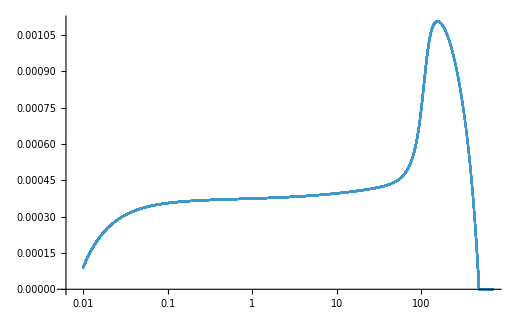

```mathematica
ListPlot[Transpose[{k*197.33,rhobar}],ScalingFunctions->{"Log",Automatic}]
```